```mathematica
Delta[a_]=a^2/3(9/(2 a^2)-1)^(2/3);
bc[a_]=1-1/3 a^2+Delta[a];
```

```mathematica
Vinflection[x_]=x^2/12(6-4a x+3 x^2)/((1+b x^2)^2)/.{a->1,b->bc[1]-10^-4}//Simplify;
```

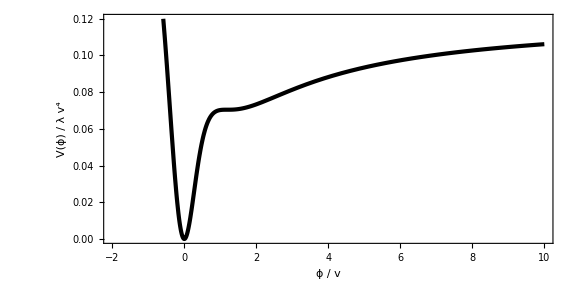

```mathematica
Plot[Vinflection[x],{x,-2,10},PlotRange->{0,0.12},PlotStyle->{Black,AbsoluteThickness[3]},FrameLabel->{Row[{ϕ," / ",v}],Row[{V[ϕ]," / ",λ v^4}]},AspectRatio->1/2]
```

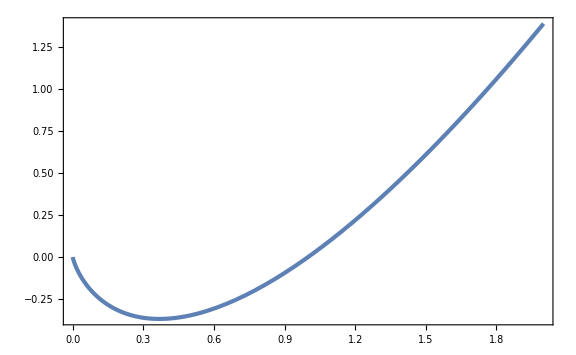

```mathematica
Plot[x Log[x],{x,0,2}]
```

```mathematica
Collect[Normal[Series[x^4(1+a Log[x]^2),{x,1,4}]],x,Simplify]
Collect[Normal[Series[(1+c(1+b Log[x])x^2)^2,{x,1,4}]],x,Simplify]
```

(11 a)/12-(14 a x)/3+(19 a x^2)/2-(26 a x^3)/3+(1+(35 a)/12) x^4

1+(11 b^2 c^2)/12+1/6 b c (1+3 c)-2/3 b c (2+(4+7 b) c) x+1/2 c (4+12 b c+19 b^2 c) x^2-2/3 b c (-2+(12+13 b) c) x^3+1/12 c (12 c+35 b^2 c+b (-2+50 c)) x^4